# Oscillateur harmonique quantique en 1D

## Definitions

```mathematica
n=4;
```

```mathematica
m=1;
```

```mathematica
h=1;
```

```mathematica
ω=10;
```

```mathematica
En[n_]:=h ω (n+1/2)
```

```mathematica
u[n_,x_]:=1/(√(2^n n!)) ((m ω)/(h π))^(1/4) ⅇ^(-(m ω x^2)/(2h)) HermiteH[n,((m ω)/h)^(1/2) x];
```

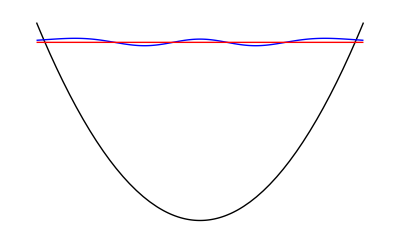

```mathematica
Plot[{1/2 m ω^2 x^2,u[n,x]+En[n],En[n]},{x,-1,1},PlotRange->{-1,50},Axes->False,PlotStyle->{Black,Blue,Red}]
```

```mathematica
Manipulate[Plot[{1/2 m ω^2 x^2,u[n,x]+En[n],En[n]},{x,-1,1},PlotRange->{-1,60},Axes->False,PlotStyle->{Black,Blue,Red}],{n,1,5,1}]
```